```mathematica
2-2
```

0

# Physicist's Introduction to Mathematica 6

## Third Edition 2007

## PHYSICS 200

Nicholas Wheeler

REED COLLEGE

## Laboratory 6

## Recursive Processes

### Background

A major shift in the way physicists think can be traced to 1972, and for a curious reason. In that year Hewlett-Packard introduced the HP-35, the first programmable calculator. It rapidly acquired the status of a cult object.  "HP-35 Clubs" appeared in scientific centers around the world. Physicists began to look forward to such dreary events as faculty meetings as opportunities to twiddle with their HP-35s, started sharing tricks (slowly—those were the days before e-mail), and interest was awakened in some mathematical phenomena that on first encounter seemed strange—the seeds of much that came after.

For example: Select a number x_0 between 0 and 1, and repeatedly hit the Cos key. What you are thus computing is

```mathematica
Cos[Cos[…[Cos[Subscript[x, 0]]]…]]
```

It was observed that the output converged to 0.739085 independently of the value you had assigned to the "seed" x_0. This result is really not unexpected in the light of the following calculation

```mathematica
FindRoot[Cos[x]==x, {x,.7}]
```

{x→0.739085}

but is unforgettably impressive when done "in the hand". It can be phrased this way: iteration of

```mathematica
map: x->Cos[x] yields 0.739085 as a fixed point
```

People tried other maps, and found that some yielded an alternating pair of fixed points:

```mathematica
a,b,a,b,a,b,a,...
```

Other maps yielded still more complicated patterns after many iterations. Some parameterized families of maps

parameterizedmap: x→f_λ[x]

were found upon iteration to possess the property that slight λ-adjustment produces radical alteration of the asymptotic pattern.  And sometimes the asymptotic output appears to be patternless/random, even though the map itself contains no element of randomness…is "deterministic;" thus did the mathematical—also (as it develops) ubiquitous physical—phenomenon of "deterministic chaos" come into focus.

Physicists soon learned to recognize instances/analogs of all of those phenomena in a wide range of physical problems. My job here will be to illustrate how Mathematica can be used to approach such subject matter—a subject matter that for the most part resists the techniques of classical analysis.

### Basic Tools

No longer is it necessary to "hit the Cos key many times." One can do so—proceed

```mathematica
Cos[0.2]
```

0.980067

```mathematica
Cos[%]
```

0.556967

```mathematica
Cos[%]
```

0.848862

```mathematica
Cos[%]
```

0.660838

```mathematica
Cos[%]
```

0.789478

```mathematica
Cos[Cos[Cos[Cos[Cos[0.2]]]]]
```

0.789478

—but Mathematica provides tools that do such things automatically: an informative introduction to this subject can be found by commanding

```mathematica
?Nest
```

Nest[f,expr,n] gives an expression with f applied n times to expr.

and following the ». Here we reproduce—with a single command—the calculation that we just did "longhand"

```mathematica
Nest[Cos[x],0.2,5]
```

0.789478

and here we just as effortlessly extend the interation to depth 100:

```mathematica
Nest[Cos[x],0.2,100]
```

0.739085

The following command

```mathematica
NestList[Cos[x],0.2,40]
```

{0.2,0.980067,0.556967,0.848862,0.660838,0.789478,0.704216,0.76212,0.723374,0.749577,0.731977,0.743854,0.735864,0.741251,0.737624,0.740068,0.738423,0.739531,0.738785,0.739288,0.738949,0.739177,0.739023,0.739127,0.739057,0.739104,0.739072,0.739094,0.739079,0.739089,0.739083,0.739087,0.739084,0.739086,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

displays the results encountered along the way, so enables you to watch the convergence. Here we do the same with a different seed:

```mathematica
NestList[Cos[x],0.9,40]
```

{0.9,0.62161,0.812942,0.687365,0.772921,0.715874,0.75452,0.728601,0.746107,0.734337,0.742275,0.736933,0.740533,0.738109,0.739742,0.738642,0.739383,0.738884,0.73922,0.738994,0.739147,0.739044,0.739113,0.739066,0.739098,0.739077,0.739091,0.739081,0.739088,0.739083,0.739086,0.739084,0.739086,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

Finally, we ask Mathematica to take the interation to however many terms it need to arrive finally at (to within its built-in margin of error) a fixed point:

```mathematica
FixedPoint[Cos[x],0.9]
```

0.739085

### Wagon's Cobweb Plot

Stan , at mathematician at Macalester College, had done a lot of clever things with Mathematica, and has an engagingly lively way of speaking/writing about them. The following bit of Mathematica Programing  is taken from page 143 of his Mathematica in Action (2nd edition, 1999):

```mathematica
CobwebPlot[f_,{x_,a_,b_},x0_,n_Integer]:=
CobwebPlot[f,{x,a,b},x0,{0,n}]
```

```mathematica
CobwebPlot[f_,{x_,a_,b_},x0_,{n0_,n_}]:=
Module[{data,fcn},
fcn=Compile[x,f];
data=NestList[fcn,s=Nest[fcn,x0,n0],n-1];
y0=If[n0==0,0,s];
Show[Block[{$DisplayFunction=Identity},
{Plot[f,{x,a,b}],
Graphics[{{Thickness[0.0005],Line[Drop[Prepend[
Flatten[
data/.z_?NumericQ:>{{z,ff=fcn[z]},{ff,ff}},1],{s,y0}],-1]]},{PointSize[0.025],Point[{s,y0}]},{GrayLevel[0.4],Line[{{a,a},{b,b}}]}}]}],PlotRange->{{a,b},All}]]
```

REMARK: Mathematica programming is a subject that will not be touched upon in these introductory labs. It is gone into in some depth in the Scientific Computing course taught by Joel Franklin & Darrell Schroeter, and can be read about in Roman Maeder's Programming in Mathematica (3rd edition) and other books.

Wagon's creation works like this

```mathematica
CobwebPlot[f[x],{x,Subscript[x, initial],Subscript[x, final]},Subscript[x, seed],number of iterations];
```

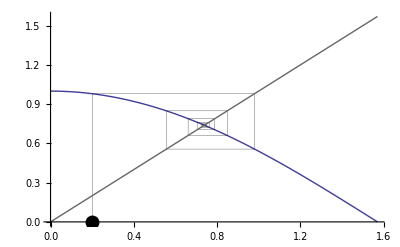

```mathematica
CobwebPlot[Cos[x],{x,0,π/2},0.2,15]
```

Let us agree to give the name "diagonal" to the straight line that passes with unit slope through (0, 0) and (1, 1); it is a graphical device for converting output f[x] into the input of f[f[x]]. The construction proceeds

```mathematica
curve->diagonal->curve->diagonal…
```

Such figures are ancient (I don't know how ancient, but were already old stuff when brought to my attention in a Reed College math class more than 50 years ago; they have been one of my favorate doodles ever since…but only fairly recently did I learn that they had anything to do with physics!)…and provide a vivid representation of the meanings both of f[f[…[f[x]]…]] and of the "iterative fixed point" concept. Such "cobwebs" are easy—and fun!—to generate with pen and paper, but successive generations of doodlers failed to notice their most interesting property.  Those come into view only with computer assistance…and soon will.  But first…

Look to our other example (same map, different seed):

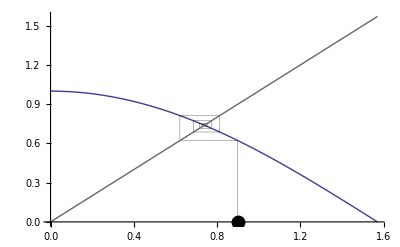

```mathematica
CobwebPlot[Cos[x],{x,0,π/2},0.9,15]
```

Try a different map:

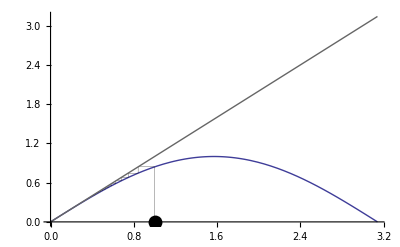

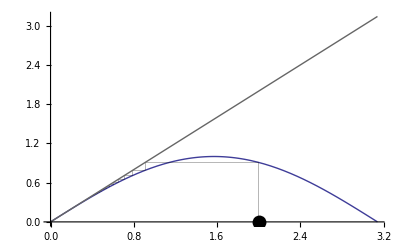

```mathematica
CobwebPlot[Sin[x],{x,0,π},1.0,15]
CobwebPlot[Sin[x],{x,0,π},2.0,15]
```

Here are the cobweb plots that result from seemingly slight variants of our most recent command:

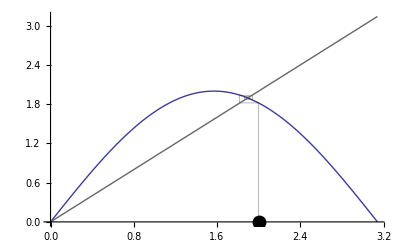

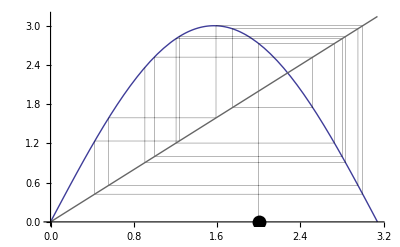

```mathematica
CobwebPlot[2Sin[x],{x,0,π},2.0,15]
CobwebPlot[3Sin[x],{x,0,π},2.0,15]
```

In the last figure no fixed point is in evidence.  CobwebPlot permits us to iterate (let us say) 275 times, but show only the last 75; to get an improved sense of what's going on, let's do so

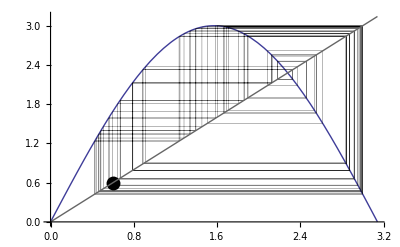

```mathematica
CobwebPlot[3Sin[x],{x,0,π},2.0,{200,75}]
```

### The Logistic Map: Bifurcation and the Onset of Chaos

In Laboratory 4 we encountered the "logistic equation" (also called the Verhulst equation)

```mathematica
x'[t]==x[t](1-x[t])
```

that models population growth with saturation (Verhulst process), which is characteristically "sigmoid":

```mathematica
DSolve[{x'[t]==x[t](1-x[t]),x[0]==0.1},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→ⅇ^t/((9.-1.10218×10^-15 ⅈ)+ⅇ^t)}}

```mathematica
logisticpopulation[t_]:=ⅇ^t/(9+ⅇ^t)
```

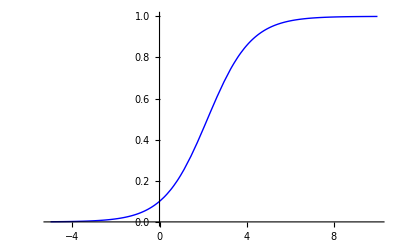

```mathematica
exact=Plot[logisticpopulation[t],{t,-5,10},PlotStyle->{RGBColor[0,0,1]}]
```

If we were motivated to solve the logistic equation numerically we would write

```mathematica
x[t+τ]=x[t]+τ x[t](1-x[t])
x[0]=0.1
```

and iterate. We are in position now to discuss very simply what would result from such a procedure:

```mathematica
Logistic[x_]:=x+1/10 x(1-x)    (*I have set τ = 1/10*)
```

```mathematica
Xvalues=NestList[Logistic,0.1,100]
```

{0.1,0.109,0.118712,0.129174,0.140423,0.152493,0.165417,0.179222,0.193933,0.209565,0.22613,0.243629,0.262056,0.281395,0.301616,0.32268,0.344536,0.367119,0.390353,0.414151,0.438414,0.463035,0.487898,0.512884,0.537867,0.562724,0.58733,0.611568,0.635323,0.658492,0.68098,0.702704,0.723595,0.743596,0.762662,0.780763,0.79788,0.814007,0.829147,0.843313,0.856527,0.868816,0.880213,0.890757,0.900488,0.909449,0.917684,0.925238,0.932155,0.938479,0.944253,0.949517,0.95431,0.958671,0.962633,0.96623,0.969493,0.97245,0.975129,0.977555,0.979749,0.981733,0.983526,0.985147,0.98661,0.987931,0.989123,0.990199,0.99117,0.992045,0.992834,0.993545,0.994187,0.994765,0.995285,0.995755,0.996177,0.996558,0.996901,0.99721,0.997488,0.997739,0.997964,0.998168,0.998351,0.998515,0.998663,0.998797,0.998917,0.999025,0.999123,0.99921,0.999289,0.99936,0.999424,0.999482,0.999534,0.99958,0.999622,0.99966,0.999694}

Here is the list of t-values that are to be associated with those x-values:

```mathematica
Tvalues=Table[i/10,{i,0,100}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2,21/10,11/5,23/10,12/5,5/2,13/5,27/10,14/5,29/10,3,31/10,16/5,33/10,17/5,7/2,18/5,37/10,19/5,39/10,4,41/10,21/5,43/10,22/5,9/2,23/5,47/10,24/5,49/10,5,51/10,26/5,53/10,27/5,11/2,28/5,57/10,29/5,59/10,6,61/10,31/5,63/10,32/5,13/2,33/5,67/10,34/5,69/10,7,71/10,36/5,73/10,37/5,15/2,38/5,77/10,39/5,79/10,8,81/10,41/5,83/10,42/5,17/2,43/5,87/10,44/5,89/10,9,91/10,46/5,93/10,47/5,19/2,48/5,97/10,49/5,99/10,10}

The following command serves very simply to create a list of lists of the desired form:

```mathematica
logisticdata=Transpose[{Tvalues,Xvalues}]
```

{{0,0.1},{1/10,0.109},{1/5,0.118712},{3/10,0.129174},{2/5,0.140423},{1/2,0.152493},{3/5,0.165417},{7/10,0.179222},{4/5,0.193933},{9/10,0.209565},{1,0.22613},{11/10,0.243629},{6/5,0.262056},{13/10,0.281395},{7/5,0.301616},{3/2,0.32268},{8/5,0.344536},{17/10,0.367119},{9/5,0.390353},{19/10,0.414151},{2,0.438414},{21/10,0.463035},{11/5,0.487898},{23/10,0.512884},{12/5,0.537867},{5/2,0.562724},{13/5,0.58733},{27/10,0.611568},{14/5,0.635323},{29/10,0.658492},{3,0.68098},{31/10,0.702704},{16/5,0.723595},{33/10,0.743596},{17/5,0.762662},{7/2,0.780763},{18/5,0.79788},{37/10,0.814007},{19/5,0.829147},{39/10,0.843313},{4,0.856527},{41/10,0.868816},{21/5,0.880213},{43/10,0.890757},{22/5,0.900488},{9/2,0.909449},{23/5,0.917684},{47/10,0.925238},{24/5,0.932155},{49/10,0.938479},{5,0.944253},{51/10,0.949517},{26/5,0.95431},{53/10,0.958671},{27/5,0.962633},{11/2,0.96623},{28/5,0.969493},{57/10,0.97245},{29/5,0.975129},{59/10,0.977555},{6,0.979749},{61/10,0.981733},{31/5,0.983526},{63/10,0.985147},{32/5,0.98661},{13/2,0.987931},{33/5,0.989123},{67/10,0.990199},{34/5,0.99117},{69/10,0.992045},{7,0.992834},{71/10,0.993545},{36/5,0.994187},{73/10,0.994765},{37/5,0.995285},{15/2,0.995755},{38/5,0.996177},{77/10,0.996558},{39/5,0.996901},{79/10,0.99721},{8,0.997488},{81/10,0.997739},{41/5,0.997964},{83/10,0.998168},{42/5,0.998351},{17/2,0.998515},{43/5,0.998663},{87/10,0.998797},{44/5,0.998917},{89/10,0.999025},{9,0.999123},{91/10,0.99921},{46/5,0.999289},{93/10,0.99936},{47/5,0.999424},{19/2,0.999482},{48/5,0.999534},{97/10,0.99958},{49/5,0.999622},{99/10,0.99966},{10,0.999694}}

That numerical data is not very easy to absorb: it would have made more sense to ask Mathematica to create but not display the data

```mathematica
newlogisticdata=Transpose[{Tvalues,Xvalues}]; (*Display turned off by final semi-colon*)
```

and then plotted the data:

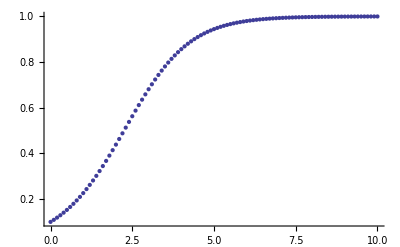

```mathematica
approximate=ListPlot[newlogisticdata]
```

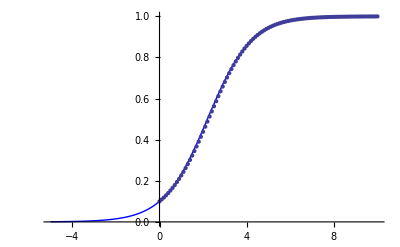

```mathematica
Show[exact,approximate]
```

Might we have taken bigger τ-steps and, with less labor, still have obtained a satisfactory result? Back up and retrace our steps:

```mathematica
Logistic2[x_]:=x+1/2 x(1-x)
```

```mathematica
Xvalues2=NestList[Logistic2,0.1,20];
Tvalues2=Table[i/2,{i,0,20}];
```

```mathematica
logisticdata2=Transpose[{Tvalues2,Xvalues2}];
```

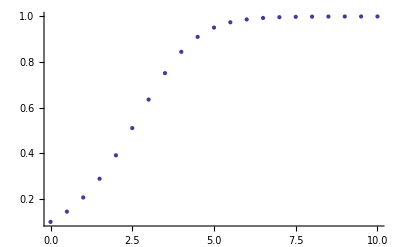

```mathematica
approximate2=ListPlot[logisticdata2]
```

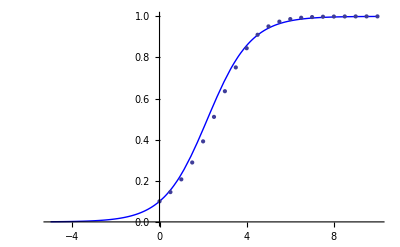

```mathematica
Show[exact,approximate2]
```

Still pretty good!…though little errors are now evident.

If we had serious interest in numerical solution of the logistic ODE we would be making τ smaller and smaller.  But—our curiosity whetted—we abandon the ODE to concentrate on the logistic map itself, looking especially to its asymptotic properties.  We try a really big τ (τ = 1.8 )

```mathematica
Logistic3[x_]:=x+1.8 x(1-x)
```

```mathematica
Xvalues3=NestList[Logistic3,0.1,50];
```

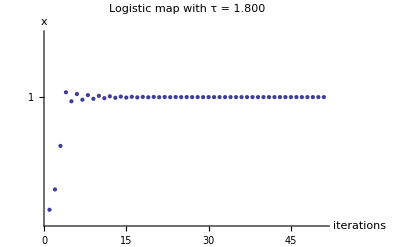

```mathematica
ListPlot[Xvalues3,PlotRange->{0,1.5},
AxesLabel->{iterations,x},
Ticks->{Automatic, {1}},PlotLabel->"Logistic map with τ = 1.800",LabelStyle->Directive[Bold,Red]]
```

and find that the iterative process still approaches 1.00000 asymptotically (as a fixed point).  But at τ = 2.0

```mathematica
Logistic4[x_]:=x+2.0 x(1-x)
```

```mathematica
Xvalues4=NestList[Logistic4,0.1,50];
```

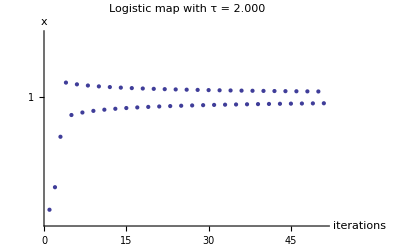

```mathematica
ListPlot[Xvalues4,PlotRange->{0,1.5},
AxesLabel->{iterations,x},
Ticks->{Automatic, {1}},PlotLabel->"Logistic map with τ = 2.000",LabelStyle->Directive[Bold,Red]]
```

we are led asymptotically to an alternating pair of points. And at τ = 2.542 (I take this value from page 5 of the 1987 thesis of Stacey Irvine)

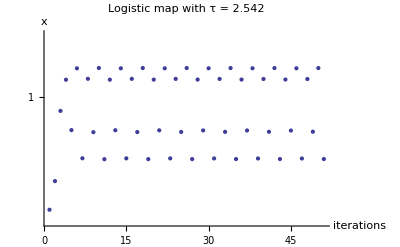

```mathematica
Logistic5[x_]:=x+2.542 x(1-x)

Xvalues5=NestList[Logistic5,0.1,50];

ListPlot[Xvalues5,PlotRange->{0,1.5},
AxesLabel->{iterations,x},
Ticks->{Automatic, {1}},PlotLabel->"Logistic map with τ = 2.542",LabelStyle->Directive[Bold,Red]]
```

we are led asymptotically to a quartet of points that present themselves in a fixed cyclic order.

CobwebPlot can be used to clarify  the situation: we define

```mathematica
logisticmap[τ_,x_]:=x+τ x(1-x)
```

and, after initially setting τ = 1.800,  proceed

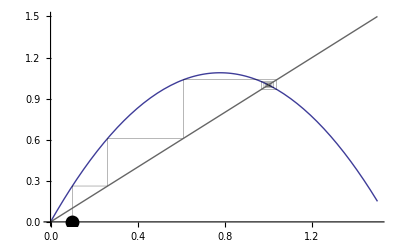

```mathematica
CobwebPlot[logisticmap[1.800,x],{x,0,1.5},0.1,50]
```

We see here a single fixed point. To get a magnified view of the last 10 steps of the 50-step iteration we command

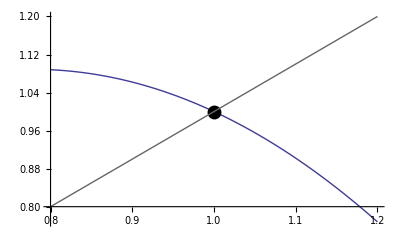

```mathematica
CobwebPlot[logisticmap[1.800,x],{x,0.8,1.2},0.1,{40,10}]
```

Now set τ = 2.000 and repeat the same steps:

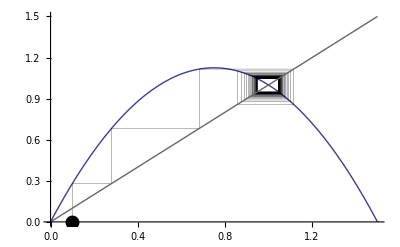

```mathematica
CobwebPlot[logisticmap[2.000,x],{x,0,1.5},0.1,50]
```

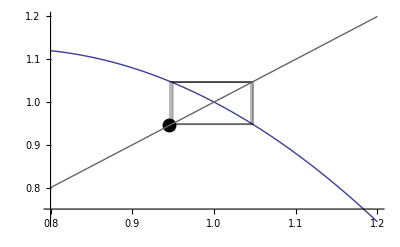

```mathematica
CobwebPlot[logisticmap[2.000,x],{x,0.8,1.2},0.1,{40,10}]
```

We find that we have in this instance become trapped in endless circulation around a box. At τ = 2.542 we end up circulating around a kind of "paperclip":

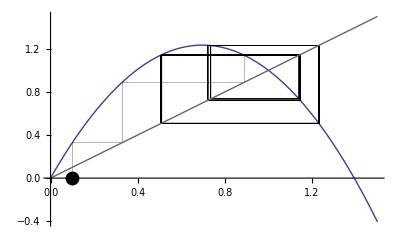

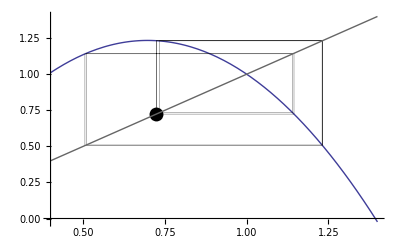

```mathematica
CobwebPlot[logisticmap[2.542,x],{x,0,1.5},0.1,50]
CobwebPlot[logisticmap[2.542,x],{x,0.4,1.4},0.1,{40,10}]
```

### Wagon's Bifurcation Plot

It becomes natural at this point to try something like the following: (1) assign a value to τ; (2) iterate long enough (say 1000 steps) until things have stabilized, then record something like 100 consecutive values; (3) increment the value of τ and do the whole thing over again; (4) plot the data thus generated.  Stacey Irvine displays just such a figure on her page 7, using C code which she presents in her Appendix A, and Stan Wagon, in his §6.4, describes how to press Mathematica into such service. Comparison would show Wagon's code (presented on his page 158) to be a good deal briefer than Irvine's.

```mathematica
Needs["Utilities`FilterOptions`"];
```

```mathematica
elimDups[v_]:=Module[{d=Sort[v]},Union[FoldList[If[#2<0.001+#1,#1,#2]&,First[d],Rest[d]]]];
```

```mathematica
Options[BifurcationPlot4]={PlotPoints->100};
```

```mathematica
BifurcationPlot4[f_,{r_,a_,b_},{x_,x0_},{iter0_,iterShow_},opts___]:=Module[{n},n=PlotPoints/.{opts}/.Options[BifurcationPlot4];makePts[{s_,v_}]:=Map[Point[{s,#}]&,v];cf=Compile[{{r,_Real,1},{x,_Real,1}},Evaluate[f]];rVals=Min[#,b]&/@Range[N[a],b,N[(b-a)/(n-1)]];data=Transpose[{rVals,elimDups/@Transpose[NestList[cf[rVals,#]&, Nest[cf[rVals,#]&,Array[x0&,n],iter0],iterShow]]}]; Show[Graphics[{AbsolutePointSize[0.4],makePts/@data}],FilterOptions[Graphics,opts],Frame->True,PlotRange->{{a,b},All}]];
```

```mathematica
BifurcationPlot=BifurcationPlot4;
```

To illustrate how Wagon's program is used—and, more interestingly, the kind of figure in which it results—we call again upon the logistic map:

```mathematica
logisticmap[τ_,x_]:=x+τ x(1-x)
```

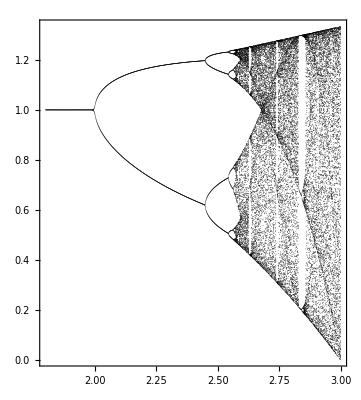

```mathematica
BifurcationPlot[logisticmap[τ,x],{τ,1.8,3},{x,0.1},{500,50},
PlotPoints->1500]  (*Beware: these calculations take a minute or so*)
```

At {500, 50} we have commanded Mathematica to do 500 iterations, then plot the results of the next 50 iterations: our intent has been to suspend the display until the iterative process has had time to stabilize if its going to stabilize.

Looking to the figure, we see that 1 is a fixed point until the control parameter τ approaches 2, when the fixed point bifurcates (this is called a "pitchfork bifurcation"). We then have a 2-cycle until τ approaches about 2.45, when a pair of second-generation bifurcations gives rise to a 4-cycle.  We then pass rapidly through ascending powers of 2 until at about τ = 2.58 we enter a chaotic regime…which appears to be punctuated occasionally with "islands of cyclicity."

If we expand the view of the 2nd & 3rd orders of bifurcation (this is done simply by reducing the distance between τ_min and τ_max) we get the impression that they are just miniature copies of the initial bifurcation; i.e., that a principle of self-similarity is operative.

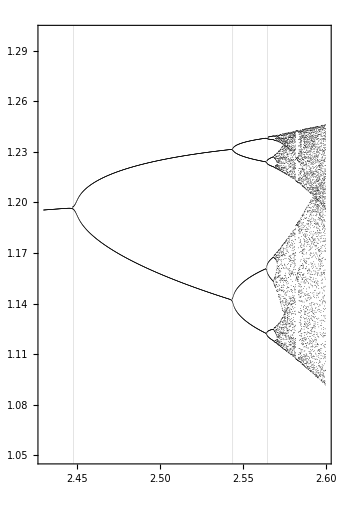

```mathematica
BifurcationPlot[logisticmap[τ,x],{τ,2.43,2.6},{x,0.1},{500,50},
PlotPoints->1500,GridLines->{{2.448,2.544,2.565},None},
PlotRange->{1.05,1.30}]
```

REMARK: If the figure, as initially presented, is scrunched up, grab a handle on the figure-box and drag to size. This will be required for several of the following figures. It was with earlier versions of this figure that I determined where to place the gridlines that mark bifurcation points. Those were improved with a couple of generations of trial and error. I have also experimented with the AspectRatio option to find ways to control Mathematica's tendency in these calculations to produce highly elongated figures.

```mathematica
?AspectRatio
```

AspectRatio is an option for Graphics and related functions which specifies the ratio of height to width for a plot.

When we try to obtain a magnified view of the first pair of "islands of cyclicity" …

```mathematica
BifurcationPlot[logisticmap[τ,x],{τ,2.6,2.8},{x,0.1},{500,50},
PlotPoints->1500,GridLines->{{2.630,2.742},None},
PlotRange->{0,1.4}, AspectRatio->1/1]
```

-Graphics-

REMARK: It is unfortunate that Wagon did not include in his program a provision for changing the aspect ratio of the figures it generates.

…we discover faint evidence of an interstitial island at about 2.70 which we look at more closely:

```mathematica
BifurcationPlot[logisticmap[τ,x],{τ,2.69,2.71},{x,0.1},{500,50},
PlotPoints->1500,GridLines->{{2.7022},None},
PlotRange->{0.2,1.3}, AspectRatio->1/1]
```

-Graphics-

Looking to the associated cobweb plot:

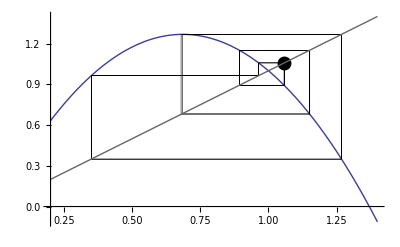

```mathematica
CobwebPlot[logisticmap[2.7022,x],{x,0.2,1.4},0.1,{200,30}]
```

we see that we have discovered a 7-cycle, which is bracketed on the left by a 6-cycle (at τ = 2.630) and on the right by a 5 cycle (at τ = 2.742).

Looking finally to a magnified view of the big 3-cycle island that lies in the neighborhood of τ = 2.84

```mathematica
BifurcationPlot[logisticmap[τ,x],{τ,2.8,2.9},{x,0.1},{500,50},
PlotPoints->1500,GridLines->{{2.841},None},
PlotRange->{0,1.4}, AspectRatio->2/1]
```

-Graphics-

we see (after dragging the figure to size) three micro-instances of the original/gross figure. This "boxes within boxes within boxes…" phenomenon—popularized by the ubiquitous —is entirely characteristic of the results that issue asymptotically from recursive processes.

#### Comparison with a Couple of Other Maps: First Glimpse of Universality

Other maps gives rise to events which—remarkably—follow the same general pattern, as I will now demonstrate. Let the logistic map

```mathematica
logisticmap[τ_,x_]:=x+τ x(1-x)
```

be replaced by the

```mathematica
quadraticmap[τ_,x_]:=τ x (1-x)
```

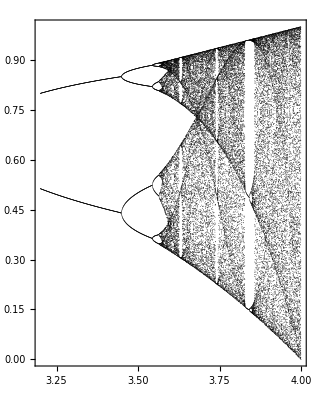

```mathematica
BifurcationPlot[quadraticmap[τ,x],{τ,3.2,4},{x,0.5},{500,50},
PlotPoints->1500,
PlotRange->{0,1.0}]
```

I can hear you say "The similarity of the figures is hardly surprising, since the maps from which they originate are so similar.'' Consider, therefore, this quite different map:

```mathematica
sinemap[τ_,x_]:=τ Sin[π x]
```

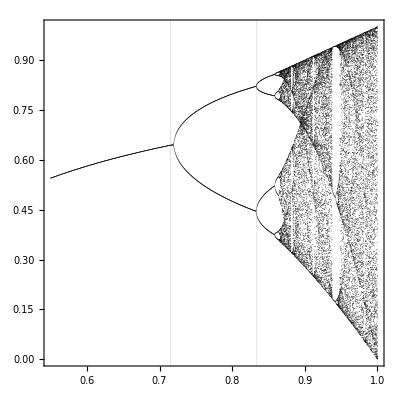

```mathematica
BifurcationPlot[sinemap[τ,x],{τ,0.55,1.0},{x,0.5},{500,50},
PlotPoints->1500,
PlotRange->{0,1},AspectRatio->1/1, GridLines->{{0.715,0.834},None}]
```

It also yields a figure of the familiar design!

The preceding figures have become icons of late 20th-Century mathematics. They speak simultaneously of

• bifurcation (successive generations of bifurcation);

• the abrupt onset of chaos (and its occasional—equally abrupt—disappearance);

• a cryptic universality.

These notions live not only in the world of mathematical abstraction; symptoms of them have been found to be all around us in the physical world, now that we have acquired eyes to see them.  They can be found in physics (in all of its flavors), biology, economics…and have become indispensable players in any modern conception of "how the world works."

## Coupled Nonlinear ODEs with Chaotic Solutions

We are in the habit of considering the world—those parts of it of greatest interest to physicists—to be described not by iterated maps but by differential equations. It has only in fairly recent times come to be widely appreciated (though it was evident to Poincare already a century ago) that fairly simple systems of coupled ODEs can have wildly irregular solutions—solutions that depend very critically upon the prescribed initial conditions. I give two examples:

### Rikitake's Model of Geomagnetic Field Reversal

In 1958, T. Rikitake (Proc. Camb. Phil. Soc. 54, 89–105) used a simple coupled disk dynamo system to model the generation of the earth's magnetic field (see §6.1 in S. Neil Rasband's Chaotic Dynamics of Nonlinear Systems (1990) for details; also the final pages of H. K. Moffatt, Magnetic Field  Generation in Electrically  Conducting Fluids (1978)).  He was led to the following system of coupled 1st order nonlinear ODEs:

x'[t]==-μ x[t]+u[t]y[t]
y'[t]==-α x[t]-μ y[t]+u[t]x[t]
u'[t]==1-x[t]y[t]

μ>0  and  α>0  are parameters

It is easy enough for Mathematica to construct numerical solutions of such coupled ODEs.  Preliminary experimentation leads us to assign illustrative values of 1.0 and 2.7 to μ and α, and initial values of 1.0, 0 and 0.5 to x, y and u; we then obtain

```mathematica
Clear[x,y,u,t]
```

```mathematica
rikitake=NDSolve[{
x'[t]==-x[t]+u[t]y[t],
y'[t]==-2.7x[t]-y[t]+u[t]x[t],
u'[t]==1-x[t]y[t],
x[0]==1.0,
y[0]==0,
u[0]==0.5},{x,y,u},{t,0,200},MaxSteps->6000]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>],u→InterpolatingFunction[{{0.,200.}},<>]}}

REMARK: Mathematica reported itself unable to do what we had commanded with the default 1000 MaxSteps value, so we increased it.

How to display the numerical information which Mathematica has now at its disposal? Rikitaki himself plotted

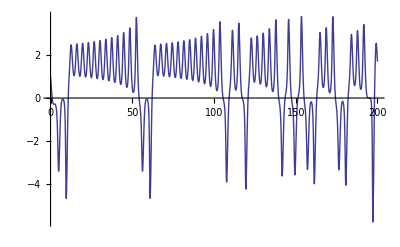

```mathematica
Plot[Evaluate[x[t]]/.%,{t,0,200},PlotRange->All]
```

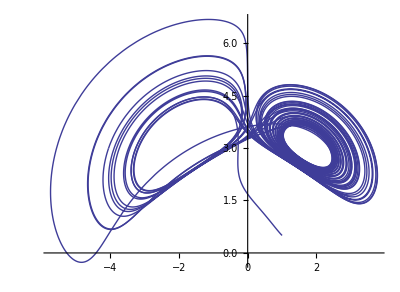

```mathematica
ParametricPlot[Evaluate[{x[t],u[t]}/.rikitake],{t,0,200},PlotPoints->3000]
```

REMARK: Without the PlotPoints → 3000 adjustment the figure would have been so kinky as to be almost unintellgible.

Those figures display, in their respective ways, the irregular sign-reversals that Rikitake (and later A. E. Cook & P. H. Roberts, "The Rikitake two-disc dynamo system," Proc. Camb. Phil. Soc. 68, 644–649 (1965)) found to be mathematically so surprising…and so suggestive of the physical facts of the matter (irregular reversals of the geomagnetic field).

In more literature one more frequently encounters figures of this design:

```mathematica
rikitakebutterfly=ParametricPlot3D[Evaluate[{x[t],y[t],u[t]}/.rikitake],{t,0,200},PlotPoints->2000,PlotRange->{{-6,4},{-5,5},{-1,9}},
AxesLabel->{"x","y","u"},
Ticks->False,
LabelStyle->Directive[Bold,Red]]
```

-Graphics3D-

INSTRUCTIONS: It is highly instructive to view the figure from several angles. Be sure to do so.

### Lorenz Model

Gentle heating of a thin layer of (say) peanut oil gives rise to orderly arrays of convection cells called . In an effort to clarify aspects of this striking phenomenon (which interested him for meteorological reasons) E. N. , in 1963, subjected the equations of fluid dynamics to radical simplification (see §5.1 and Appendix A in Heinz Schuster's book, mentioned above; for Lorenz' original paper see "Deterministic nonperiodic flow," J. Atmos. Sci 20, 130) and obtained equations

x'[t]==-σ x[t]+σ y[t]
y'[t]==r x[t]-y[t]-r x[t]z[t]
z'[t]==x[t]y[t]-b z[t]

σ>0,r  and  b>0  are parameters

Lorenz introduced the picturesque phrase "butterfly effect" to refer to a remarkable property of this system (and,  as it turns out, many other systems) of coupled nonlinear ODEs: infinitesimally different intial conditions typically tin finite time to radially different solutions.

REMARK: I provide here a link to an excellent applet, prepared by the San Francisco Exploratorium, which lets you experiment with your own instances of Lorenz's .

Selecting parameters that are discovered by experiment to place us in the "interesting part" of parameter space, we proceed exactly as before

```mathematica
Clear[x,y,u,t]
```

```mathematica
lorenz=NDSolve[{
x'[t]==-3x[t]+3y[t],
y'[t]==26.5x[t]-y[t]-u[t]x[t],
u'[t]==x[t]y[t]-u[t],
x[0]==0,
y[0]==1,
u[0]==0},{x,y,u},{t,0,20},MaxSteps->3000]
```

{{x→InterpolatingFunction[{{0.,20.}},<>],y→InterpolatingFunction[{{0.,20.}},<>],u→InterpolatingFunction[{{0.,20.}},<>]}}

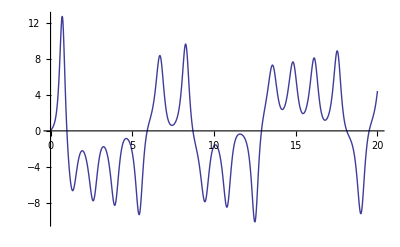

```mathematica
Plot[Evaluate[x[t]]/.%,{t,0,20},PlotRange->All]
```

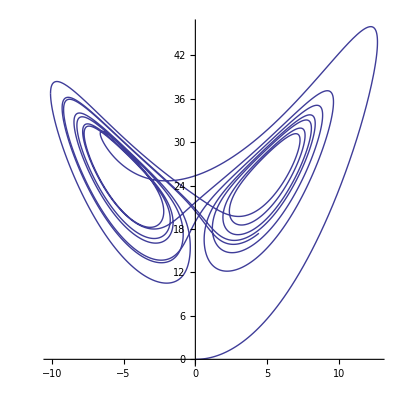

```mathematica
ParametricPlot[Evaluate[{x[t],u[t]}/.lorenz],{t,0,20},PlotPoints->3000,AspectRatio->1/1]
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],u[t]}/.lorenz],{t,0,20},PlotPoints->2000,
AxesLabel->{"x","y","u"},
Ticks->False,
LabelStyle->Directive[Bold,Red], AspectRatio->Automatic]
```

-Graphics3D-

The qualitative resemblance to results obtained from the (much less well-known) Rikitake model is striking. We again detect the scent of some kind of "universality" principle…in which connection we note that both systems are (not obviously, the way I have presented them) nonlinear forced dissipative systems.

I will not pursue this rich topic, because to do so would risk being seduced by the physics, and our present assignment is simply to become acquainted with the utility of Mathematica. So I leave the Poincare maps, Liapunov exponents, etc. for you to explore on your own, if someday you are so inclined.

You will appreciate that DEs are like iterated maps, in that they tell the state point where to go, where to go, where to go… And that such rich structure as we have seen is exposed only by numerical analysis (which Mathematica takes in easy stride).  And the moral of it all: simple rules can have inexhaustibly complex consequences.

## Fitting Curves to Data

### Preliminary Remarks

It is increasingly rare for your activity in the laboratory to be describable as "hands-on" production of "raw data." For it has become commonplace for a computer (else built-in special-purpose software) to stand between you and the measurement device, interpreting your intentions to the device, and reporting back a pre-digested account of what the device has detected. Which is OK if the software works, and if you know the true meaning of its reports.

But occasionally you find yourself in the classical situation of

• trying to make statistical sense of tabulated experimental data;

• trying to make statistical sense of tabulated experimental data;

Concerning the first issue: Mathematica is general purpose mathematical software, not a "statistics engine." Mathematica does, however, come with elaborate built-in statistical capabilities—go to Documention Center, look at the box labeled Data Handling & Data Sources, then search for guide/Statistics for basic information and tutorials—and many statistical packages add in various ways to that capability.

### Importing Data

It is valuable in this connection to know how to import data into Mathematica. This is not difficult…the essential command being

```mathematica
?Import
```

Import[file] imports data from a file, returning a complete Mathematica version of it. 
Import[file,elements] imports the specified elements from a file.
Import[http://url,…] and Import[ftp://url,…] imports from any accessible URL.

To demonstrate how this works, I have deposited a file named SedonaMorning.jpg in the Mathematica Manuals folder on the Courses Server. To import that file, first write the incomplete command

```mathematica
Import[]
```

Then go to Insert > File Path…  The "Select a file" window will open showing all accessible files, and at the bottom of which are found a Cancel button and a Choose button.  Select  Blossoms.jpg file and—with the cursor blinking at the ⋀ in the Import[ ] command—hit the Choose button: the desired file "path" will be inserted between the square brackets, as shown below. Execute the command (i.e., hit ⌤) and an imported copy of the file will appear.

```mathematica
Import["/Volumes/QUANTUM/SedonaMorning.jpg"]
```

-Graphics-

The imported file now lives in the notebook, and would remain there even if the source file were destroyed.

I will not attempt to survey here the powerful resources that Mathematica places at your disposal for the analysis of images, acoustic signals and digital data : you have, by now, learned a bit about how consult the vast Mathematica literature (much of it at your electronic fingertips), and will best be instructed by urgent necessity as occasions arise.

I look instead to some techniques having to do with the graphical display of digital data (but will not concern myself with the production of bar graphs, pie charts, etc.—stuff that Mathematica also knows how to do, but that physicists seldom find useful).

### Curve Fitting Techniques

I follow in the steps of Stan Wagon, who treats this subject in his Chapter 11. We begin by creating some artificial "data":

```mathematica
data=Table[{x,Sin[x]-Cos[x]+Log[1+x^2]},{x,0,12,1}]//N
```

{{0.,-1.},{1.,0.994316},{2.,2.93488},{3.,3.4337},{4.,2.73005},{5.,2.01551},{6.,2.37133},{7.,3.81511},{8.,5.30925},{9.,5.72997},{10.,4.91017},{11.,3.79961},{12.,3.59631}}

Try first a decorated variant of the ListPlot command, a simple device which we encountered already in Lab 1:

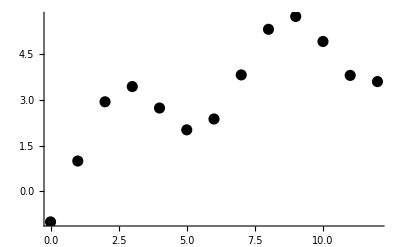

```mathematica
rawdatapoints=ListPlot[data,Epilog->{PointSize[0.02],Point/@data}]
```

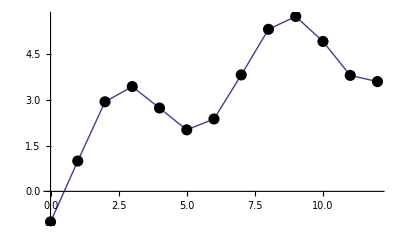

```mathematica
ListPlot[data,Epilog->{PointSize[0.02],Point/@data},PlotJoined->True]
```

Here as always—when mystified by details in a sample command (here: the PlotJoined option, the use of Epilog  and the meaning of /@), we can ask Mathematica about them:

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
?Epilog
```

Epilog is an option for graphics functions which gives a list of graphics primitives to be rendered after the main part of the graphics is rendered.

```mathematica
?/@
```

RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] or RowBox[{StyleBox["f", "TI"], "/@", StyleBox["expr", "TI"]}] applies StyleBox["f", "TI"] to each element on the first level in StyleBox["expr", "TI"]. 
RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"].

Just as easy to use, but in most applications more interesting—and certainly more powerful (it contains the preceding as a special case, as we will see)—is the command

```mathematica
?Interpolation
```

RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation of the function values SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]], assumed to correspond to StyleBox["x", "TI"] values 1, 2, … . 
RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation of the function values SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]] corresponding to StyleBox["x", "TI"] values SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]].
RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation of multidimensional data.
RowBox[{"Interpolation", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["df", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] constructs an interpolation that reproduces derivatives as well as function values.

that asks Mathematica to use its smarts to come up with a "best" interpolation (which Mathematica does by using piecewise cubic curves; we'll see in a moment what that means):

```mathematica
func=Interpolation[data]
```

InterpolatingFunction[{{0.,12.}},<>]

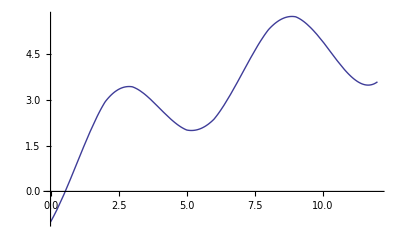

```mathematica
fittedcurve=Plot[Evaluate[func[x]],{x,0,12}]
```

To see how well the curve conforms to the data, we consturct this composite figure:

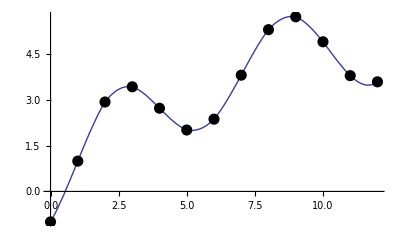

```mathematica
Show[{fittedcurve,rawdatapoints},Epilog->{PointSize[0.02],Point/@data}]
```

We should remember, however, that infinitely many alternative curves also thread precisely through the prescribed set of points.

When asked to extrapolate from the given data, Mathematica reminds you that extrapolation is intrinsically hazardous:

InterpolatingFunction::dmval: Input value {-1.99967} lies outside the range of data in the interpolating function. Extrapolation will be used.

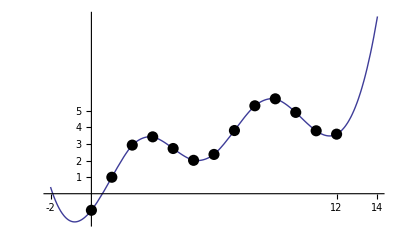

```mathematica
Plot[Evaluate[func[x]],{x,-2,14},
Epilog->{PointSize[0.02],Point/@data}, Ticks->{{-2,12,14},{1,2,3,4,5}}]
```

The interpolated function can, for most purposes, be treated like any other function; thus

```mathematica
func[10]
```

4.91017

```mathematica
∫_0^12 func[x]ⅆx
```

39.3819

```mathematica
FindRoot[func[x]==4,{x,6}]
```

{x→7.1116}

When we ask Mathematica about

```mathematica
Options[Interpolation]
```

{InterpolationOrder→3,PeriodicInterpolation→False}

we are informed that (as previously remarked) Interpolation uses cubics by default, the implication being that we might elect to proceed otherwise.   Try

```mathematica
func1=Interpolation[data,InterpolationOrder->1]
```

InterpolatingFunction[{{0.,12.}},<>]

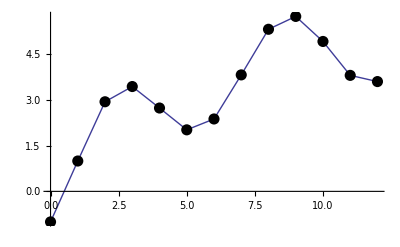

```mathematica
Plot[Evaluate[func1[x]],{x,0,12},
Epilog->{PointSize[0.02],Point/@data}]
```

and discover that we have simply reproduced the effect of PlotList with PlotJoined→True . We have, in particular, not managed to fit a straight line to the entire data set (the Interpolation procedure acts "piecewise"). That, however, can be accomplished in the least squares sense

```mathematica
∑_(data points) (data-linear approximant)^2=minimum
```

```mathematica
?Fit
```

RowBox[{"Fit", "[", RowBox[{StyleBox["data", "TI"], ",", StyleBox["funs", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] finds a least-squares fit to a list of data as a linear combination of the functions StyleBox["funs", "TI"] of variables StyleBox["vars", "TI"].

The {1, x} in the command

```mathematica
linearFit=Fit[data,{1,x},x]
```

1.03763+0.348089 x

signals that we have asked Mathematica to do its best to fit the data to a curve of the form

```mathematica
Subscript[a, 0]+Subscript[a, 1] x
```

—which is just what Mathematica did.  Look at the result:

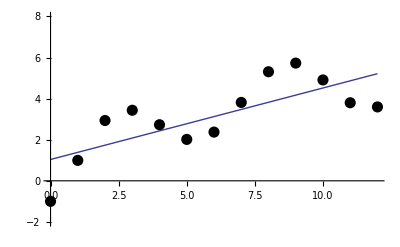

```mathematica
Plot[linearFit,{x,0,12},Epilog->{PointSize[0.02],Point/@data},
PlotRange->{-2,8}]
```

Try a 4th order polynomial:

```mathematica
quadricFit=Fit[data,{1,x,x^2,x^3,x^4},x]
```

-1.01331+3.32767 x-1.0303 x^2+0.131547 x^3-0.00554079 x^4

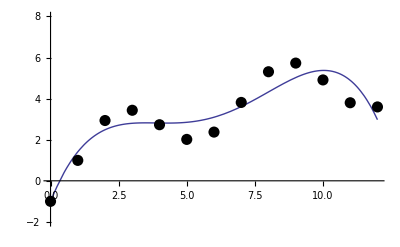

```mathematica
Plot[quadricFit,{x,0,12},Epilog->{PointSize[0.02],Point/@data},
PlotRange->{-2,8}]
```

Try 8th order:

```mathematica
degreeEightFit=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

-0.999216+1.2016 x+1.1881 x^2-0.333239 x^3-0.113406 x^4+0.0529201 x^5-0.0075335 x^6+0.000465605 x^7-0.0000107219 x^8

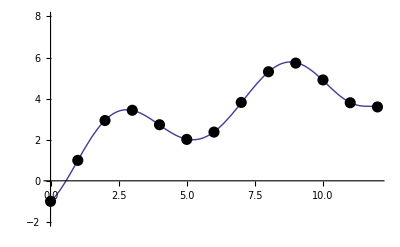

```mathematica
Plot[degreeEightFit,{x,0,12},Epilog->{PointSize[0.02],Point/@data},
PlotRange->{-2,8}]
```

We know we would enjoy perfect success in 13th order (since there are 13 data points), but it's a little remarkable that we did so well in 8th.

It's important, however, to realize that we are not married to polynomials: a mathematician with superhuman insight might try

```mathematica
devilsFit=Fit[data,{Sin[x],Cos[x],Log[1+x^2]},x]
```

-1. Cos[x]+1. Log[1+x^2]+1. Sin[x]

and thus recover precisely the function we originally used to generate our toy data! A less insightful mathematician might have tried (say)

```mathematica
devilsapprenticeFit=Fit[data,{Sin[x],Cos[x],1,x^2},x]
```

1.79717+0.0276635 x^2-1.3743 Cos[x]+0.895377 Sin[x]

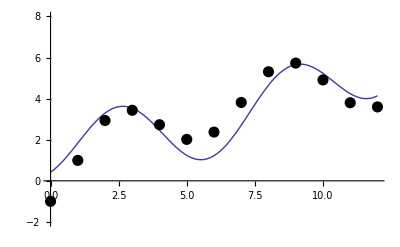

```mathematica
Plot[devilsapprenticeFit,{x,0,12},Epilog->{PointSize[0.02],Point/@data},
PlotRange->{-2,8}]
```

### Fourier Analytic Curve Fitting

Suppose our data were known/suspected on some grounds to be periodic:

```mathematica
periodicdata={{1.,2.5},{2.,1.994315859499702},{3.,2.9348821758069246},{4.,3.4336975976543584},{5.,2.7300544696118996},{6.,2.0155100778951174},{7.,2.3713321277949326},{8.,3.8151073498036303},{9.,5.309245550327632},{10.,5.7299679943906865},{11.,4.910170935028343},{12.,3.7996051401945024},{13.,3.596306865687647},{14.,2.5},{15.,1.994315859499702},{16.,2.9348821758069246},{17.,3.4336975976543584},{18.,2.7300544696118996},{19.,2.0155100778951174},{20.,2.3713321277949326},{21.,3.8151073498036303},{22.,5.309245550327632},{23.,5.7299679943906865},{24.,4.910170935028343},{25.,3.7996051401945024},{26.,3.596306865687647}};
```

The method I used to generate that data is of no particular interest. This is what is looks like:

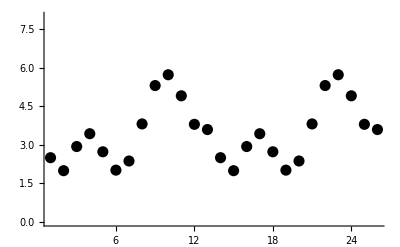

```mathematica
ListPlot[periodicdata,PlotRange->{0,8},Epilog->{PointSize[0.02],Point/@periodicdata}]
```

It seems to repeat with period 13, so we try

```mathematica
fourierFit=Fit[periodicdata,{
Cos[0(2π)/13 x],Sin[0(2π)/13 x],
Cos[1(2π)/13 x],Sin[1(2π)/13 x],
Cos[2(2π)/13 x],Sin[2(2π)/13 x],
Cos[3(2π)/13 x],Sin[3(2π)/13 x],
Cos[4(2π)/13 x],Sin[4(2π)/13 x]},x]
```

3.47232+0.289565 Cos[(2 π x)/13]-0.854991 Cos[(4 π x)/13]+0.42387 Cos[(6 π x)/13]+0.162705 Cos[(8 π x)/13]-1.28257 Sin[(2 π x)/13]-0.304402 Sin[(4 π x)/13]+0.0566442 Sin[(6 π x)/13]+0.108922 Sin[(8 π x)/13]

The following figure

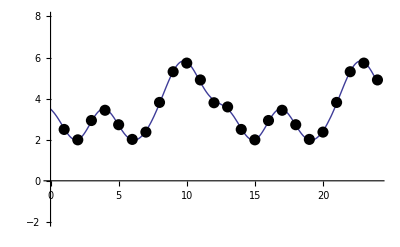

```mathematica
Plot[fourierFit,{x,0,24},Epilog->{PointSize[0.02],Point/@periodicdata},
PlotRange->{-2,8}]
```

shows the result to be quite good (which is not at all remarkable, since we have used 10 functions to fit 13 data points).

On the following evidence

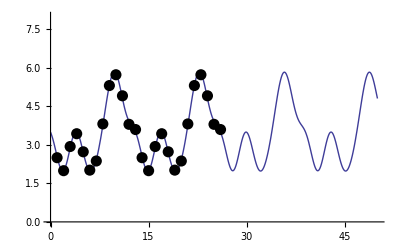

```mathematica
Plot[fourierFit,{x,0,50},Epilog->{PointSize[0.02],Point/@periodicdata},
PlotRange->{0,8}]
```

we infer that Mathematica, though reluctant to extrapolate on the basis of Interpolate, is happy to do so on the basis of information produced by Fit .